# Chess tactics for beginners

Progetto di Matematica computazionale per l’anno accademico 2022/2023.
Collaborators: Andrea Accornero, Andrea Bianchi, Mattia Frega, Gabriele Magazzù.

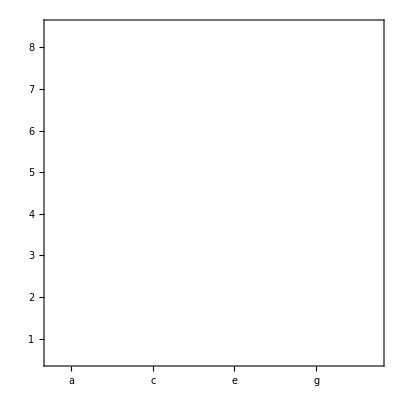

```mathematica
cb[n_] := MatrixPlot[
  Range@ConstantArray[n, n] + Range[n],
  ColorFunction -> GrayLevel,
  ColorFunctionScaling -> False,
  PlotRangePadding -> None,
  FrameTicks -> {
   {#, #} &@ Table[{i, n - i + 1, 0}, {i, n}],
   {#, #} &@ Table[{i, FromCharacterCode[ToCharacterCode["a"] + i - 1], 0}, {i, n}]},
  FrameStyle -> Bold]

cb[8]
```